```mathematica
(*Definisci i valori di m e n*)nQubs=6;
jj=2^(nQubs-1);
mm=jj;
nn=jj-2;

f[m_, n_, phi_]:=If[0<phi<Pi/2||3*Pi/2<phi<2*Pi,Exp[I*(-m+n)*phi]/(2*Pi),-Exp[I*(-m+n)*phi]/(2*Pi)]

integrale=NIntegrate[f[mm, nn, phi],{phi,0,2*Pi}];

integrale
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in phi near {phi} = {6.2831852790070679749612623856117770478751927143434841127600520849}. NIntegrate obtained -4.64039×10^-17+3.46945×10^-18 ⅈ and 4.89812×10^-14 for the integral and error estimates.

-4.64039×10^-17+3.46945×10^-18 ⅈ

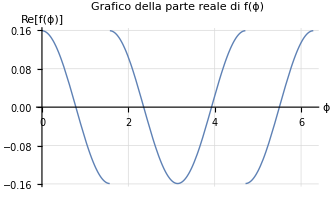

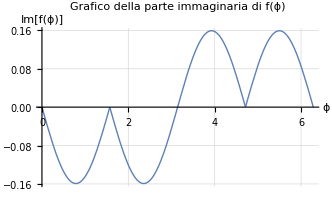

```mathematica
(*Traccia il grafico della parte reale di f(phi)*)
Plot[Re[f[mm, nn, phi]],{phi,0,2*Pi},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ϕ","Re[f(ϕ)]"},PlotLabel->"Grafico della parte reale di f(ϕ)",GridLines->Automatic]

(*Traccia il grafico della parte immaginaria di f(phi)*)
Plot[Im[f[mm, nn, phi]],{phi,0,2*Pi},PlotRange->All,PlotStyle->Thick,AxesLabel->{"ϕ","Im[f(ϕ)]"},PlotLabel->"Grafico della parte immaginaria di f(ϕ)",GridLines->Automatic]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.77556×10^-17 and 9.77557×10^-17 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {1.5707962986223783009641881426199410331720485167750211985548958182}. NIntegrate obtained -8.2833×10^-17 and 4.893×10^-14 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {1.5707963831399330720685027431273914338277775115670920058619230986}. NIntegrate obtained 6.07153×10^-18 and 1.23598×10^-13 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in φ near {φ} = {2.81725×10^-8}. NIntegrate obtained -1.19262×10^-16 and 5.56492×10^-14 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::eincr: The global error of the strategy GlobalAdaptive has increased more than 400 times. The global error is expected to decrease monotonically after a number of integrand evaluations. Suspect one of the following: the working precision is insufficient for the specified precision goal; the integrand is highly oscillatory or it is not a (piecewise) smooth function; or the true value of the integral is 0. Increasing the value of the GlobalAdaptive option MaxErrorIncreases might lead to a convergent numerical integration. NIntegrate obtained -2.77556×10^-17 and 9.77557×10^-17 for the integral and error estimates.

General::stop: Further output of NIntegrate::eincr will be suppressed during this calculation.

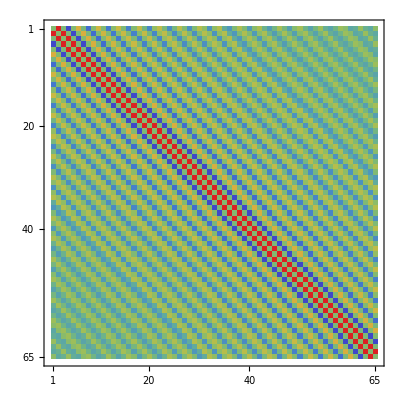

{65,65}

```mathematica
nQubs=6;
jj=2^(nQubs-1);

(*Definizione della funzione f con la parte reale*)f[mm_,nn_,phi_]:=Re[If[0<phi<Pi/2||3*Pi/2<phi<2*Pi,Exp[I*(-mm+nn)*phi]/(2*Pi),-Exp[I*(-mm+nn)*phi]/(2*Pi)]]

ttt=Table[Table[NIntegrate[f[mm,nn,φ],{φ,0,2*π}],{mm,-jj,jj}],{nn,-jj,jj}];

ttt//Chop;
MatrixPlot[ttt,ColorFunction->"Rainbow"]
```

Part::partw: Part 14 of {8,16,32,64,128,256,512,1024,2048,4096,«3»} does not exist.

Part::partw: Part 15 of {8,16,32,64,128,256,512,1024,2048,4096,«3»} does not exist.

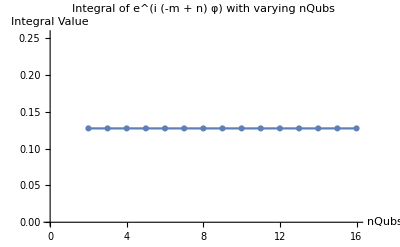

```mathematica
nQubsMax=16;

jVals=Table[2^(nQubs - 1)         ,{nQubs,4,nQubsMax}];

(*Calcola i valori di ttt*)
ttt=Table[Module[{jj=jVals[[nQubs-1]],mm,nn},mm=Evaluate[jj];
nn=Evaluate[jj-5];
{nQubs,Abs[NIntegrate[f[mm,nn,φ],{φ,0,2 π}]]}],{nQubs,2,nQubsMax}];

(*Plot dei risultati*)
ListLinePlot[ttt,PlotMarkers->Automatic,AxesLabel->{"nQubs","Integral Value"},PlotLabel->"Integral of e^(i (-m + n) φ) with varying nQubs"]
```